```mathematica
x
```

x

```mathematica
ImportDataset["5to50_40_10000_randomnew.mx"]
```

```mathematica
Clear[x,lengths]
```

```mathematica
lengths =x;
```

x

```mathematica
lengths
```

{k[k][k][k[s]]→3,s[k][s][k[s]]→4,k[k][k[k][s]]→3,18426,s[s][s[k][s[s[k][k[s]]][k[k[s]][s[s][s[s]][s][s]][s[s][k[k][s][k][k]]]][s[k[k]][k[k][s[s][k]]]][s[k]]][k[s][k[s][s[s][k]][k[k][s]][s[s][s[k][s]]]]]]→5,s[s[s[k][s]]][s[s[s]][s[s[s]]][k[s]][k[k][k[s]]][k[s][k][s[s[k[k]][s][s[s][s][s]]]][k[s][s[s[k[s[s][k[k[k]]]]]][k[s[k]][k[s[s]][k[k][k][k[s]]]]]]]]]→13}
 |  |  |  |

```mathematica
!(13===False)
```

True

```mathematica
DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/10_40_15000_randomnew_varlengths.mx",lengths];
```

```mathematica
NoHalt = Select[lengths,#[[2]]==False&];
Halt = Select[lengths,!(#[[2]]=== False)&];
Length[NoHalt]
Length[Halt]
```

728

17703

```mathematica
HaltTrain = RandomSample[Halt,Length[NoHalt]];
```

```mathematica
HaltTrain[[1]]
```

s[k[s[k[s[k[k[s]]]]][k[s[k[s]][s[s]]]][s[k][s[k]][k]][k[s[s]][k]]]]→True

```mathematica
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
```

```mathematica
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
```

```mathematica
RasterTrain = Join[HaltTrainRaster,NoHaltTrainRaster];
```

```mathematica
DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/5to50_40_10000_rastertrain.mx",RasterTrain];
```

```mathematica
RasterTrain
```

```mathematica
RasterPredict=RasterTrain/.(a_->b_)/;b===False:> (a->0);
```

```mathematica
RasterPredict
```

```mathematica
DumpSave["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/SK-Combinators/5to50_40_10000_rasterpredict.mx",RasterPredict];
```

```mathematica
RasterPredictor=Predict[RasterPredict]
```

MapThread::mptd: Object LinearLayer[1,Weights→{{0.000684376,-0.000390617,-0.000656525,«45»,-0.0000356685,0.000852142,«2344»}},Biases→{0.},Input→2394][«18»[«1»]] at position {2, 1} in MapThread[PDF,{LinearLayer[1,Weights→{{0.000684376,-0.000390617,«47»,0.000852142,«2344»}},Biases→{0.},Input→2394][NormalDistribution[{«1»},«19»]],{«1»}}] has only 0 of required 1 dimensions.

Join::heads: Heads List and LinearLayer[1,Weights→{{0.000684376,-0.000390617,-0.000656525,«45»,-0.0000356685,0.000852142,«2344»}},Biases→{0.},Input→2394] at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and LinearLayer[1.,Weights→{{0.000684376,-0.000390617,-0.000656525,«45»,-0.0000356685,0.000852142,«2344»}},Biases→{0.},Input→2394.] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

MapThread::mptd: Object LinearLayer[1,Weights→{{0.000684376,-0.000390617,-0.000656525,«45»,-0.0000356685,0.000852142,«2344»}},Biases→{0.},Input→2394][«18»[«1»]] at position {2, 1} in MapThread[PDF,{LinearLayer[1,Weights→{{0.000684376,-0.000390617,«47»,0.000852142,«2344»}},Biases→{0.},Input→2394][NormalDistribution[{«1»},«19»]],{«1»}}] has only 0 of required 1 dimensions.

MapThread::mptd: Object LinearLayer[1.,Weights→{{0.000684376,-0.000390617,-0.000656525,«45»,-0.0000356685,0.000852142,«2344»}},Biases→{0.},Input→2394.][«1»] at position {2, 1} in MapThread[PDF,{LinearLayer[1.,Weights→{{0.000684376,-0.000390617,-0.000656525,«46»,0.000852142,«2344»}},Biases→{0.},Input→2394.][«18»[«1»]],«1»}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
Export["10_40_15000_raster_classify.wmlf",RasterClassify]
```

10_40_15000_raster_classify.wmlf

0.818 accuracy (RandomForest) ... but is it just classifying based on the lines given?
0.758 accuracy with 5 lines.

0.8 accuracy with 5 lines for new random model

```mathematica
RasterMeasurements=ClassifierMeasurements[RasterClassify,RasterTest]
```

ClassifierMeasurementsObject[…]

```mathematica
RasterMeasurements["Accuracy"]
```

0.817805

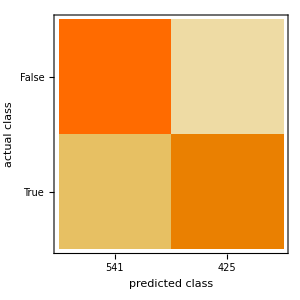

```mathematica
RasterMeasurements["ConfusionMatrixPlot"]
```

What about accuracy for other leaf sizes?

```mathematica
LeafSize40 = CreateTrainingData[x];
```

```mathematica
RasterMeasurements40 = ClassifierMeasurements[RasterClassify,LeafSize40]
```

ClassifierMeasurementsObject[…]

```mathematica
RasterMeasurements40["Accuracy"]
```

0.819444

```mathematica
LeafSize30 = CreateTrainingData[x];
```

```mathematica
RasterMeasurements30 = ClassifierMeasurements[RasterClassify,LeafSize40]
```

ClassifierMeasurementsObject[…]

```mathematica
RasterMeasurements30["Accuracy"]
```

0.819444

#### Table of Results

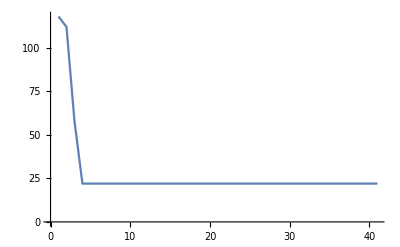
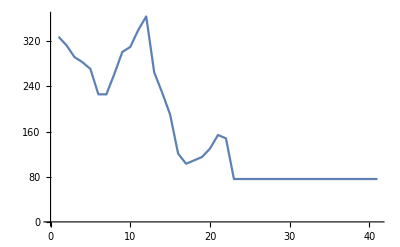
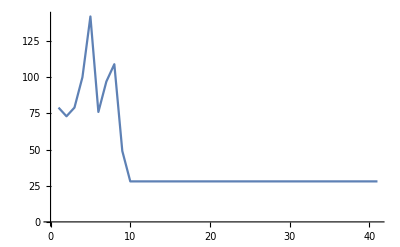
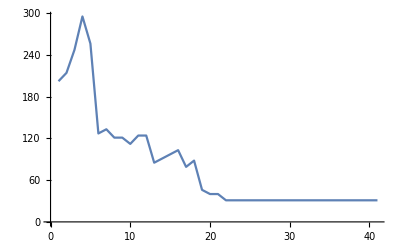
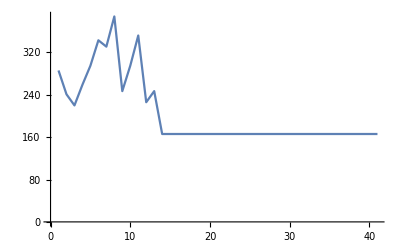
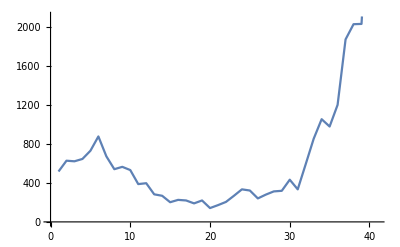
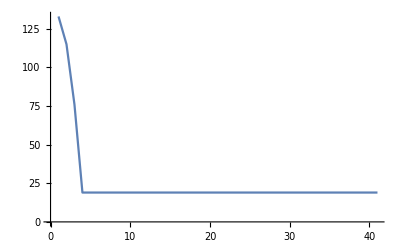
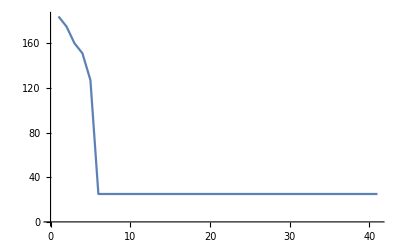
{{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{False,-Graphics-,False},{True,-Graphics-,False},{True,-Graphics-,False}}

```mathematica
Table[TestClassifierRasterize[RasterClassify,RasterTrain],50]
```

#### Thoughts

Perhaps it’s training on the last few lines of the raster. Try feature set identification:

```mathematica
rasternet = NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
rasterfeatureFunction=Take[rasternet,{1,"fc7"}]
```

NetChain[<>]

```mathematica
rastertraining = Keys[RasterTrain];
```

```mathematica
rasterfeatures=Monitor[Table[rasterfeatureFunction[rastertraining[[x]]],{x,1,Length[rastertraining]}],x];
```

```mathematica
xyz = DimensionReduce[features,3,Method->"TSNE"];
Graphics3D[
MapThread[Inset[Thumbnail[RemoveBackground@#2,32],#1]&,{xyz,rastertraining}],
BoxRatios->{1, 1, 1}
]
```

DimensionReduce::mlmpty: The dataset should contain at least one example.

MapThread::mptd: Object DimensionReduce[features,3,Method→TSNE] at position {2, 1} in MapThread[Inset[Thumbnail[RemoveBackground[#2],32],#1]&,{DimensionReduce[features,3,Method→TSNE],rastertraining}] has only 0 of required 1 dimensions.

-Graphics3D-

$Aborted

$Aborted